# Лекция 1

## Переменные

### Скалярные

Переменные рекомендуется называть строчными буквами, т.к. c прописных букв начинаются название встроенных функций

```mathematica
a=1
```

1

По-умолчанию Математика показывает (по возможности) точный результат выражений

```mathematica
{1/153,√2}
```

{1/153,√2}

Для вывода приближенного значения используется функция N

```mathematica
N[1/153,4]
N[1/153,7]
```

0.006536

0.006535948

Если в выражении встречается вещественное число (с точкой), то и результат будет приближенный

```mathematica
1/153.
```

0.00653595

Подавление вывода результата

```mathematica
a=1;
```

```mathematica
{π,e,I,∞,Degree,°}
```

{π,e,ⅈ,∞,°,°}

```mathematica
{%,%%,%%%}
```

{{π,e,ⅈ,∞,°,°},1,0.00653595}

```mathematica
ClearAll[a]
ClearAll["Global`*"]
a=.
```

Palettes -> Basic Math Assistant

## Ввод чисел с другим основанием

В двоичной системе

```mathematica
2^^101
```

5

В шестнадцатеричной системе

```mathematica
16^^FF
```

255

Функция BaseForm преобразовывает число из одной системы в другую

5 в десятичной системе преобразуется в двоичную

```mathematica
BaseForm[5,2]
```

101_2

222, записанное в двоичной системе преобразуется в десятичную систему

```mathematica
BaseForm[2^^11011110,10]
```

222

IntegerDigits

```mathematica
IntegerDigits[531]
```

{5,3,1}

```mathematica
N[1/153,20]
```

0.0065359477124183006536

```mathematica
RealDigits[1/153]
```

{{{6,5,3,5,9,4,7,7,1,2,4,1,8,3,0,0}},-2}

## Отложенное присвоение

```mathematica
a=c;
a:=c;
```

Выражение, записанное справа от знака отложенного присвоения вычисляется только тогда, когда это необходимо

## Отложенное присвоение

```mathematica
a=c
```

c

```mathematica
c=3;
a
```

3

```mathematica
a:=2c+10
c=1;
a
```

12

```mathematica
c = 2;
a
```

14

## Отложенное присвоение

Правая часть вычисляется, только когда требуется

```mathematica
a:=Random[]
```

```mathematica
a
```

0.185966

Обращение к a приводит к вычислению нового случайного числа

```mathematica
a
```

0.0777446

## Двумерная запись

```mathematica
b:=2
```

c[Ctrl][-]3:=6

```mathematica
Subscript[c, 3]:=6
```

```mathematica
Subscript[a, 3]
```

0.822555_3

```mathematica
a/6
```

0.000925274

a[Ctrl][/]6

```mathematica
a/6
```

0.153945

[Ctrl][2]a

```mathematica
√a
```

0.936272

## Интервалы

```mathematica
mass=Interval[{0.9,1.1}];
work=Interval[{9,10}];
velocity=√((2 work)/mass)
```

Interval[{4.0452,4.71405}]

```mathematica
velocity[[1]]
```

{4.0452,4.71405}

```mathematica
√(2*9/1.1)
```

4.0452

## Списки

#### Одномерные

```mathematica
a={10,20,30,40,50}
```

{10,20,30,40,50}

```mathematica
a[[2]]
```

20

```mathematica
a[[{3,4}]]
```

{30,40}

```mathematica
Part[a,{3,4}]
```

{30,40}

```mathematica
a[[2;;4]]
```

{20,30,40}

## Списки

```mathematica
a = {10, 20, 30, 40, 50}
```

{10,20,30,40,50}

```mathematica
First[a]
```

10

```mathematica
Last[a]
```

50

```mathematica
Rest[a]
```

{20,30,40,50}

```mathematica
Most[a]
```

{10,20,30,40}

```mathematica
Drop[a,2]
```

{30,40,50}

```mathematica
Select[a,10<=#≤30&]
```

{10,20,30}

## Многомерные списки

```mathematica
a={{10,20,30},{40,50,60},{80,60,30},{41,56,67}}
```

{{10,20,30},{40,50,60},{80,60,30},{41,56,67}}

```mathematica
MatrixForm[a]
```

(10 | 20 | 30
40 | 50 | 60
80 | 60 | 30
41 | 56 | 67)

```mathematica
a[[2,3]]
```

60

```mathematica
MatrixForm[a[[{2, 3}, {1,3}]]]
```

(40 | 60
80 | 30)

```mathematica
MatrixForm[a[[{2,3},1;;3]]]
```

(40 | 50 | 60
80 | 60 | 30)

## Генерация списков

### Range

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Range[3,5]
```

{3,4,5}

```mathematica
Subdivide[0,1,5]
```

{0,1/5,2/5,3/5,4/5,1}

## Генерация списков

### Table

```mathematica
Table[i^2,{i,2,10}]
```

{4,9,16,25,36,49,64,81,100}

```mathematica
Table[i^2,{i,2,10,2}]
```

{4,16,36,64,100}

```mathematica
Table[{i,i^2},{i,2,10,2}]
```

{{2,4},{4,16},{6,36},{8,64},{10,100}}

```mathematica
Table[10 i+j,{i,1,3},{j,2,8,2}]
```

{{12,14,16,18},{22,24,26,28},{32,34,36,38}}

## Генерация списков

```mathematica
IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Table[If[i==j,1,0],{i,1,3},{j,1,3}]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
ConstantArray[3,5]
```

{3,3,3,3,3}

```mathematica
Table[3,{5}]
```

{3,3,3,3,3}

## Преобразование списков

```mathematica
a=Table[i^2,{i,2,10,2}]
```

{4,16,36,64,100}

```mathematica
Reverse[a]
```

{100,64,36,16,4}

```mathematica
Join[{1,2},{3,4}]
```

{1,2,3,4}

```mathematica
{Min[a],Max[a]}
```

{4,100}

```mathematica
{a+a,a*a,a/a}
```

{{8,32,72,128,200},{16,256,1296,4096,10000},{1,1,1,1,1}}

```mathematica
a={3,4};
b={1,2};
a^b
```

{3,16}

## Добавление и удаление элементов

```mathematica
a=Table[i^2,{i,2,10,2}]
```

{4,16,36,64,100}

```mathematica
{Append[{1,2,3},30],Prepend[{1,2,3},30]}
```

{{1,2,3,30},{30,1,2,3}}

```mathematica
{Insert[{1,2,3,4},17,2],Insert[{1,2,3,4},17,-2]}
```

{{1,17,2,3,4},{1,2,3,17,4}}

```mathematica
RotateLeft[a]
```

{16,36,64,100,4}

```mathematica
RotateRight[a]
```

{100,4,16,36,64}

## Сортировка

```mathematica
a=RandomInteger[{-10,10},4]
Sort[a]
f[a_,b_]:=a>b;
Sort[a,f]
Sort[a,#1>#2&]
```

{-3,0,-5,5}

{-5,-3,0,5}

{5,0,-3,-5}

{5,0,-3,-5}

```mathematica
data={{x, 2}, {y, 1}, {z, 5}};
```

```mathematica
Sort[data,#1[[2]]<#2[[2]]&]
```

{{y,1},{x,2},{z,5}}

```mathematica
a
Ordering[a]
Ordering[a,2]
Ordering[a,-2]
```

{8,-9,2,1}

{2,4,3,1}

{2,4}

{3,1}

```mathematica
a=Table[0,{5},{5}];
a//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
a[[All,2]]=1;
a[[;;,2]]=1;
a//MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0)

```mathematica
a[[All,2]]=Range[5];
a//MatrixForm
```

(0 | 1 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0
0 | 4 | 0 | 0 | 0
0 | 5 | 0 | 0 | 0)

```mathematica
a[[1;;2,3;;4]]=({{1, 2}, {3, 4}});
a//MatrixForm
```

(0 | 1 | 1 | 2 | 0
0 | 2 | 3 | 4 | 0
0 | 3 | 0 | 0 | 0
0 | 4 | 0 | 0 | 0
0 | 5 | 0 | 0 | 0)

```mathematica
AppendTo[a,{7,8,9,10,11}]
a//MatrixForm
```

{{0,1,1,2,0},{0,2,3,4,0},{0,3,0,0,0},{0,4,0,0,0},{0,5,0,0,0},{7,8,9,10,11}}

(0 | 1 | 1 | 2 | 0
0 | 2 | 3 | 4 | 0
0 | 3 | 0 | 0 | 0
0 | 4 | 0 | 0 | 0
0 | 5 | 0 | 0 | 0
7 | 8 | 9 | 10 | 11)

```mathematica
Do[AppendTo[a[[i]],9],{i,1,6}]
a//MatrixForm
```

(0 | 1 | 1 | 2 | 0 | 9
0 | 2 | 3 | 4 | 0 | 9
0 | 3 | 0 | 0 | 0 | 9
0 | 4 | 0 | 0 | 0 | 9
0 | 5 | 0 | 0 | 0 | 9
7 | 8 | 9 | 10 | 11 | 9)

## Partition

```mathematica
Partition[{a,b,c,d,e,f},2]
```

{{a,b},{c,d},{e,f}}

```mathematica
Partition[{a,b,c,d,e,f},2,1]
```

{{a,b},{b,c},{c,d},{d,e},{e,f}}

## Tuples & Subsets

```mathematica
Tuples[{1,2,3},2]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

```mathematica
Subsets[{1,2,3},2]
```

{{},{1},{2},{3},{1,2},{1,3},{2,3}}

```mathematica
Subsets[{1,2,3},{2}]
```

{{1,2},{1,3},{2,3}}

```mathematica
Subsets[{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]},{Subscript[x, 4],Subscript[y, 4]},{Subscript[x, 5],Subscript[y, 5]}}, {3}]
```

{{{x_1,y_1},{x_2,y_2},{x_3,y_3}},{{x_1,y_1},{x_2,y_2},{x_4,y_4}},{{x_1,y_1},{x_2,y_2},{x_5,y_5}},{{x_1,y_1},{x_3,y_3},{x_4,y_4}},{{x_1,y_1},{x_3,y_3},{x_5,y_5}},{{x_1,y_1},{x_4,y_4},{x_5,y_5}},{{x_2,y_2},{x_3,y_3},{x_4,y_4}},{{x_2,y_2},{x_3,y_3},{x_5,y_5}},{{x_2,y_2},{x_4,y_4},{x_5,y_5}},{{x_3,y_3},{x_4,y_4},{x_5,y_5}}}

## Pattern

```mathematica
a={1,2,3.0,4,5.0,6,7,{1,3}};
```

```mathematica
Count[a,_List]
```

1

```mathematica
Count[a,_Integer]
```

5

```mathematica
Count[a,a_/;a>5 || a<2]
Cases[a,a_/;a>5 || a<2]
```

3

{1,6,7}

```mathematica
a={"fd",1,2,3,"4"}
Position[a,_String]
Cases[a,_String]
```

{fd,1,2,3,4}

{{1},{5}}

{fd,4}

```mathematica
Count[{y^3,1,2,3,x^-1,x,x^2,x^3},a_^b_/;b==-1]
Position[{y^3,1,2,3,x^-1,x,x^2,x^3},a_^b_/;b==2]
Cases[{y^3,1,2,3,x^-1,x,x^2,x^3},a_^b_/;b==2]
```

1

{{7}}

{x^2}

```mathematica
Table[Random[Real,{0,100},3],{10}]
Count[%,a_/;a<30]
```

{81.3,26.1,13.6,97.8,13.,1.64,97.3,41.6,25.3,88.5}

5

## Векторы

```mathematica
a={1,2,3};
b={3,4,5};
```

```mathematica
a.b
```

26

```mathematica
Cross[a,b]
```

{-2,4,-2}

```mathematica
Norm[a]
```

√14

```mathematica
Projection[a,b]
```

{39/25,52/25,13/5}

```mathematica
(a.b)/Norm[b] b/Norm[b]
```

{39/25,52/25,13/5}

## Функции

#### Объявление функций

Встроенные функции Математики начинаются с большой буквы

```mathematica
{Sin[2],N[Sin[2]],Sin[2.0]}
```

{Sin[2],0.909297,0.909297}

```mathematica
hyp=Function[{x,y},√(x^2+y^2)]
```

Function[{x,y},√(x^2+y^2)]

```mathematica
hyp[1,3]
```

√10

```mathematica
Clear[hyp]
hyp[x_,y_]=√(x^2+y^2)
```

√(x^2+y^2)

x_ -- некое значение, которое мы будем называть при определении функции “x”

```mathematica
hyp[x_,y_]:=√(x^2+y^2)
```

## Анонимная функция

Через анонимную функцию

```mathematica
hyp=√(#1^2+#2^2)&;
hyp[1,2]
```

√5

Пример (почему это может быть удобно)

```mathematica
√2//N[#,10]&
```

1.414213562

Sort, Select

hyp = lambda x, y: math.sqrt(x**2+y**2)

## Постфиксная, префиксная и инфиксная запись

Постфиксная запись

```mathematica
12//Sin
```

Sin[12]

```mathematica
√2//N[#,10]&
```

1.414213562

## Постфиксная, префиксная и инфиксная запись

Инфиксная запись

```mathematica
2~Plus~1
```

3

Префиксная запись

```mathematica
Sin@d
```

Sin[d]

Функциональная запись

```mathematica
Sin[1.2]
```

0.932039

## Функции с индексами

Функции с индексами

```mathematica
f[1][x_,y_]=x+y;
f[2][x_,y_]=x-y;

f[RandomInteger[{1,2}]][1,2]
```

3

```mathematica
Subscript[f, 1][x_,y_]=x+y;
Subscript[f, 2][x_,y_]=x-y;
Subscript[f, RandomInteger[{1,2}]][1,2]
```

3

## Значения по умолчанию

```mathematica
f[x_,y_:10]:=10x+y;
f[10]
f[10,20]
```

110

120

## Кусочные функции

```mathematica
f[x_]:=If[x>0,1,-1]
```

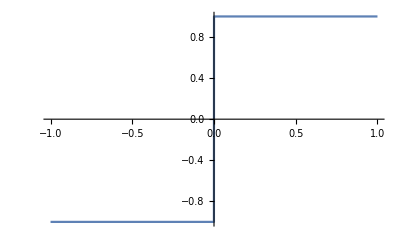

```mathematica
g[x_]:=1/;x>0
g[x_]:=-1/;x<=0
Plot[g[x],{x,-1,1}]
```

## Замены

Замена

```mathematica
d+3+√(h+1)
```

3+d+√(1+h)

```mathematica
d+3+√(h+1)/.{d->3,h->5}
```

6+√6

Показать в приближенном виде:

```mathematica
N[d+3+√(h+1)/.{d->3,h->5}]
```

8.44949

```mathematica
{a1,b1,c1,d1}/.a1->10
```

{10,b1,c1,d1}

```mathematica
{a1,b1,c1,d1}/.{a1->10,c1->20}
```

{10,b1,20,d1}

## Отложенная замена

```mathematica
{a1,a1,a1}/.a1->RandomReal[]
{a1,a1,a1}/.a1:> RandomReal[]
```

{0.637502,0.637502,0.637502}

{0.563525,0.408296,0.534081}

## Функции и списки

```mathematica
q={1,2,3,4,5}
Sin[q]
```

{1,2,3,4,5}

{Sin[1],Sin[2],Sin[3],Sin[4],Sin[5]}

```mathematica
f[x_]:=x^2+3*Sin[x]
f[q]
```

{1+3 Sin[1],4+3 Sin[2],9+3 Sin[3],16+3 Sin[4],25+3 Sin[5]}

```mathematica
f=.
f[x_]:=Total[x]
f[q]
```

15

```mathematica
Map[f,{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
f/@{1,2,3}
```

{f[1],f[2],f[3]}

## Apply

```mathematica
Apply[f,{1,2,3}]
f@@{1,2,3}
```

f[1,2,3]

f[1,2,3]

Apply для первого уровня

```mathematica
Apply[f,{{1,2},{2,3},{3,4}},{1}]
f@@@{{1,2},{2,3},{3,4}}
```

{f[1,2],f[2,3],f[3,4]}

{f[1,2],f[2,3],f[3,4]}

```mathematica
Apply[ss[#2,#1]&,{{1,2},{2,3},{3,4}},{1}]
ss[#2,#1]&@@@{{1,2},{2,3},{3,4}}
```

{ss[2,1],ss[3,2],ss[4,3]}

{ss[2,1],ss[3,2],ss[4,3]}

```mathematica
Total[{{1,2},{3,4},{5,6,7}}]
```

Total::tllen: Lists of unequal length in {{1,2},{3,4},{5,6,7}} cannot be added.

Total[{{1,2},{3,4},{5,6,7}}]

```mathematica
Total[{{1,2},{3,4},{5,6}}]
```

{9,12}

```mathematica
#1^2+#2*10&@@@{{1,2},{3,4},{5,6}}
```

{21,49,85}

## Map

```mathematica
Map[Apply[Plus,#]& ,{{1,2},{3,4},{5,6,7}}]
```

{3,7,18}

```mathematica
Apply[Plus,#]& /@{{1,2},{3,4},{5,6,7}}
```

{3,7,18}

#### Select

```mathematica
a={1,2,3,4,5};
Select[a,#>3&]
```

{4,5}